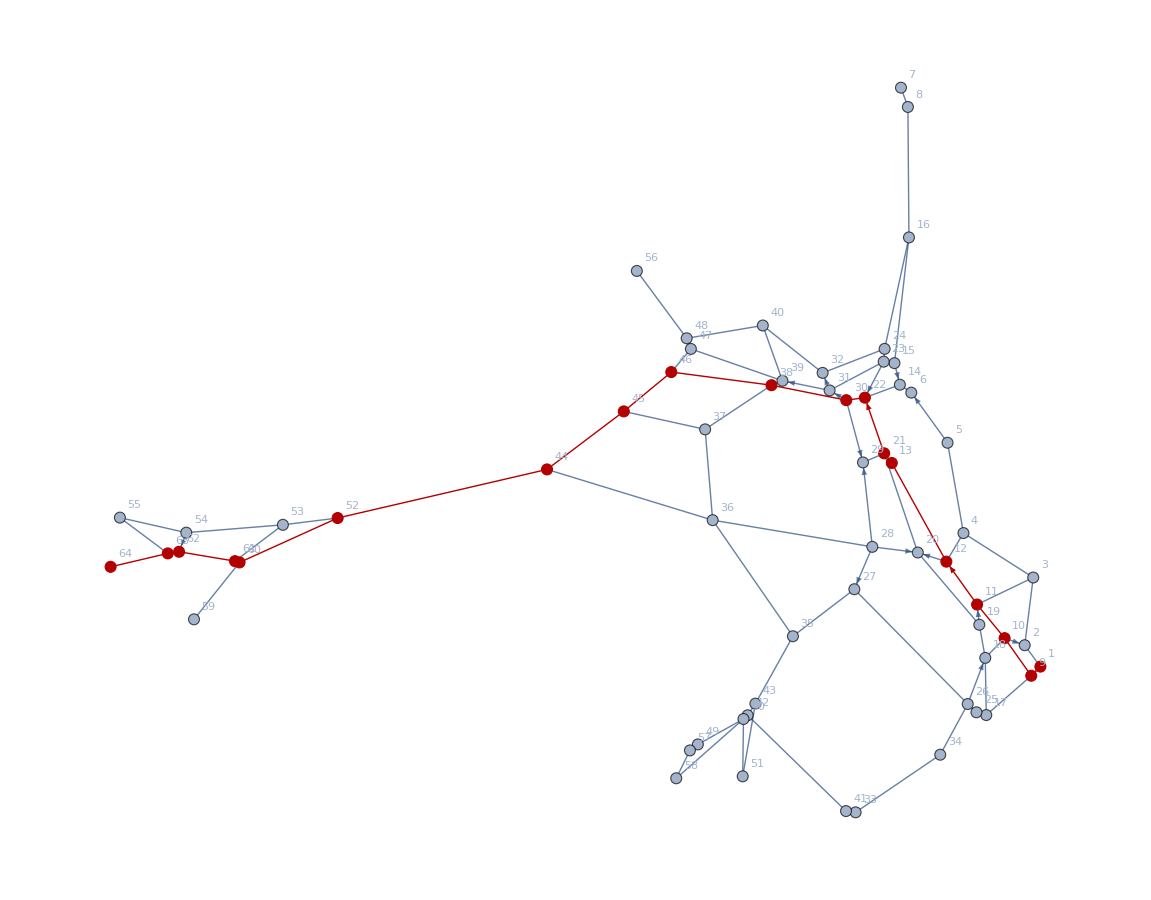

```mathematica
Ded={{25,17,2},{10,2,3},{26,18,5},{15,14,3},{50,42,1},{19,11,3},{23,22,4},{28,27,4},{28,20,4},{30,29,5},{1,9,3},{5,6,6},{11,12,4},{21,22,5},{12,20,3},{28,29,6},{30,31,2},{31,32,3},{47,48,2},{54,62,4},{31,39,4},{60,61,1}};

Ued={{1,2,2},{2,3,5},{9,17,4},{3,4,5},{4,5,4},{33,41,1},{7,8,2},{49,57,1},{9,10,3},{10,11,2},{10,18,2},{12,13,5},{26,34,3},{15,16,6},{50,58,6},{17,18,5},{3,11,6},{18,19,2},{19,20,6},{20,21,5},{27,35,3},{35,43,3},{43,51,5},{23,24,1},{25,26,1},{4,12,2},{26,27,6},{28,36,6},{36,44,6},{44,52,6},{52,60,5},{33,34,5},{13,21,1},{35,36,6},{21,29,2},{36,37,5},{37,38,4},{37,45,5},{38,39,1},{39,40,5},{53,61,5},{41,42,6},{6,14,1},{42,43,1},{14,22,2},{22,30,1},{44,45,4},{30,38,4},{45,46,3},{38,46,5},{46,47,2},{49,50,3},{50,51,6},{15,23,1},{23,31,5},{52,53,3},{53,54,5},{39,47,4},{54,55,5},{55,63,6},{57,58,3},{8,16,6},{16,24,6},{59,60,5},{24,32,6},{32,40,5},{61,62,3},{40,48,6},{62,63,1},{48,56,5},{63,64,4}};

{v1,v2,v3,v4}={1,64,22,52};

(*Edge lists*)
directedEdgeList=Map[Function[x,DirectedEdge[Part[x,1],Part[x,2]]],Ded];
undirectedEdgeList=Map[Function[x,UndirectedEdge[Part[x,1],Part[x,2]]],Ued];
(*subGraphs*)
directedSubgraph=Graph[directedEdgeList];
undirectedSubgraph=Graph[undirectedEdgeList];

(*graphs  union*)
graph=GraphUnion[directedSubgraph,undirectedSubgraph];

(*вес*)
For[i=1,i≤Length[Ded],i++,
graph=SetProperty[{graph,directedEdgeList⟦i⟧},EdgeWeight->Ded⟦i⟧⟦3⟧];
]

For[i=1,i≤Length[Ued],i++,
graph=SetProperty[{graph,undirectedEdgeList⟦i⟧},EdgeWeight->Ued⟦i⟧⟦3⟧];
]

graph=SetProperty[graph,VertexLabels->"Name"];
graph=SetProperty[graph,GraphLayout->{VertexLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}}];
graph;

w={1->2,2->3,3->4,4->5,2->5};
graph1=Graph[w];

(*Adjacency matrix*)
adjacencyMatrix=WeightedAdjacencyMatrix[graph];

maxValue=999999;
For[i=1,i≤Length[adjacencyMatrix],i++,
For[j=1,j≤Length[adjacencyMatrix⟦i⟧],j++,
If[adjacencyMatrix⟦i⟧⟦j⟧==0,adjacencyMatrix⟦i⟧⟦j⟧=maxValue]
]
]


(*Путь v1->v2 Dijkstra*)
vertex=v1;
vertices={};
AppendTo[vertices,vertex];
(*Distance array init for starting vertex v1*)
distances={};
pathVertices={};

For[v=1,v≤Length[adjacencyMatrix⟦vertex⟧],v++,
AppendTo[pathVertices,vertex];
If[v==vertex,
AppendTo[distances,0];,
AppendTo[distances,adjacencyMatrix⟦vertex⟧⟦v⟧];

]
]
distances;
For[i=1,i<Length[distances],i++,
minValue=maxValue;

For[v=1,v<=Length[distances],v++,
If[!MemberQ[vertices,v]&&minValue>distances⟦v⟧,
minValue=distances⟦v⟧;
vertex=v;
];
];

AppendTo[vertices,vertex];
Clear[v];
(*diistances recalc*)
For[v=1,v<=Length[distances],v++,
adjacencyMatrix⟦vertex⟧⟦v⟧
If[!MemberQ[vertices,v],
If[distances⟦v⟧>distances⟦vertex⟧+adjacencyMatrix⟦vertex⟧⟦v⟧,pathVertices⟦v⟧=vertex];
distances⟦v⟧=Min[distances⟦v⟧,distances⟦vertex⟧+adjacencyMatrix⟦vertex⟧⟦v⟧];
;]
]
]

path={};
v=v2;
PrependTo[path,v];
While[v≠v1,
v=pathVertices⟦v⟧;
PrependTo[path,v];
];
(*Create *)

distances//ColumnForm;
vertices;
path;

pathGraph=GraphUnion[PathGraph[path],PathGraph[path,{DirectedEdges->True}]];
highlightedGraph=HighlightGraph[graph,pathGraph]
highlightedGraph=HighlightGraph[highlightedGraph,PathGraph[path,{DirectedEdges->True}]];
```